## Fussmann bifurcation diagram

### Data import

```mathematica
(* Set directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/hopf_fussmann_2000"];
```

```mathematica
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Import data *)
rawdataChlor=Import["bifurcation_code/fussmann_bif_c.dat"];
rawdataBrach=Import["bifurcation_code/fussmann_bif_b.dat"];

(* convert chlorella from μmol/lit to cells/ml *)
rawdataChlor[[;;,{2,3}]]=rawdataChlor[[;;,{2,3}]]*50000;
(* convert brachionus from μmol/lit to females/ml *)
rawdataBrach[[;;,{2,3}]]=rawdataBrach[[;;,{2,3}]]*5;
```

### Info and Setup

Stability representation in .dat file:
	1 - stable node
	2 - unstable node
	3 - stable limit cycle
	4 - unstable limit cycle

```mathematica
legendLine=LineLegend[{Black,{Black,Dashed},Blue,{Blue,Dashed}},{"Stable node","Unstable node","Stable limit cycle","Unstable limit cycle"}]
```

### Figure parameters

```mathematica
lt=0.004; (* line thickness *)
imgs=900; (* image size *)
aRatio=0.22; (* aspect ratio *)
deltaVals={0.04,0.32,0.64,0.95,1.24,1.37}; (* dilution rates of selected time-series *)
```

### Chlorella Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdataChlor[[;;,{1,2,4,5}]],rawdataChlor[[;;,{1,3,4,5}]]]//DeleteDuplicates;
```

```mathematica
(* Stability type of point i *)
stabType=fulldata[[;;,3]];
```

```mathematica
numPoints=Length[fulldata];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldata[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldata⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* investigate each node section *)
Table[ListLinePlot[nodeSections[[i,;;,{1,2}]],PlotRange->{{0,2},{0,4.2}*1000000},
PlotLabel->ToString[i],
PlotStyle->TMBcolours[[1]],
InterpolationOrder->1,
PlotRange->{{0,2},{0,4.2}*1000000},
Frame->True],{i,1,23}];
```

```mathematica
(* split seciton 15 into two and move one chunk to 16 *)
nodeSections[[16]]=nodeSections[[15,1829;;-1]];
nodeSections[[15]]=nodeSections[[15,1;;1827]];
```

```mathematica
(* take relevant branch numbers *)
branchesNums={2,4,6,9,13,15,16,19,23};
```

```mathematica
(* clear out points that go beyond max dilution rate on plot *)
nodeSections2=Table[DeleteCases[nodeSections[[i]],{x_,_,_,_}/;x>1.5],{i,1,Length[nodeSections]}];
```

```mathematica
(* pick out x and y values in relevant branches for bifurcation plot and export *)
bifPtsChlorella=Table[nodeSections2[[i,;;,{1,2}]],{i,branchesNums}];
Export["data/bifPtsChlor.mat",bifPtsChlorella];
```

```mathematica
bifPlotChlorella=ListLinePlot[bifPtsChlorella,
PlotStyle->Table[{TMBcolours[[1]],Thickness[lt]},{i,1,Length[branchesNums]}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,4.2}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlorella vulgaris (10^6 cells/ml)",Style["Brachionus calyciflorus (females/ml)",White]},{"","Dilution rate δ (per day)"}},
FrameTicks->{{Transpose[{Range[-4/40,4]*1000000,Range[0,4]}],None},{Automatic,Range[0,2,0.2]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
PlotRangeClipping->False,
ImagePadding->{{50,50},{30,50}},
Epilog->{Directive[{Black}],
Line[Table[{Scaled[{0,-0.1},{deltaVals[[i]],0}],
Scaled[{0,0.1},{deltaVals[[i]],0}]},{i,1,Length[deltaVals]}]],
Text[Style["a",14,Bold],Scaled[{0.02,0.9}]]}]
```

-Graphics-

### Brachionus Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdataBrach[[;;,{1,2,4,5}]],rawdataBrach[[;;,{1,3,4,5}]]]//DeleteDuplicates;
```

```mathematica
(* Stability type of point i *)
stabType=fulldata[[;;,3]];
```

```mathematica
numPoints=Length[fulldata];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldata[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldata⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* investigate each node section *)
Table[ListLinePlot[nodeSections[[i,;;,{1,2}]],PlotRange->{{0,2},{0,55}},
PlotLabel->ToString[i],
PlotStyle->TMBcolours[[1]],
InterpolationOrder->1,
Frame->True],{i,1,Length[nodeSections]}];
```

```mathematica
nodeSections[[14]]=nodeSections[[13,1;;2045]];
nodeSections[[13]]=nodeSections[[13,2048;;-1]];
```

```mathematica
(* take relevant branch numbers *)
branchesNums={2,4,6,9,13,14,17};
```

```mathematica
(* clear out points that go beyond max dilution rate on plot *)
nodeSections2=Table[DeleteCases[nodeSections[[i]],{x_,_,_,_}/;x>1.5],{i,1,Length[nodeSections]}];
```

```mathematica
(* pick out x and y values in relevant branches for bifurcation plot, and export *)
bifPtsBrachionus=Table[nodeSections2[[i,;;,{1,2}]],{i,branchesNums}];
Export["data/bifPtsBrach.mat",bifPtsBrachionus];
```

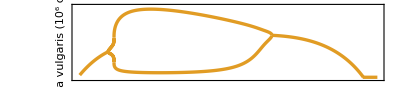

```mathematica
bifPlotBrachionus=ListLinePlot[bifPtsBrachionus,
PlotRange->{{0,1.5},{-59/40,59}},
PlotStyle->Table[{TMBcolours[[2]],Thickness[lt]},{i,1,Length[branchesNums]}],
LabelStyle->14,
InterpolationOrder->1,
Frame->{{False,True},{True,True}},
FrameLabel->{{Style["Chlorella vulgaris (10^6 cells/ml)",White],"Brachionus calyciflorus (females/ml)"},{"",""}},
FrameTicks->{{None,Range[0,60,10]},{None,None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
ImagePadding->{{50,50},{30,50}}]
```

### Combined bifurcation plot

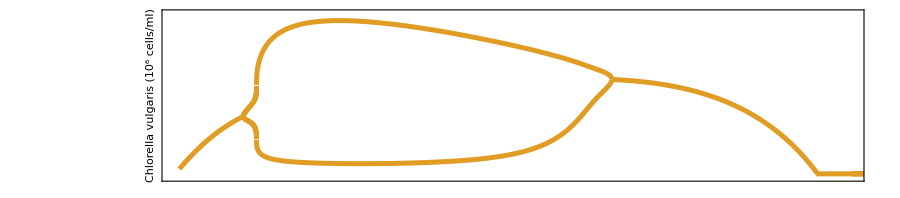
-Graphics--Graphics-

```mathematica
bifPlotFussmann=Overlay[{bifPlotChlorella,bifPlotBrachionus}]
```

```mathematica
(*Export["figures/bif_fussmann_redo.png",bifPlotFussmann,ImageResolution->200];*)
```